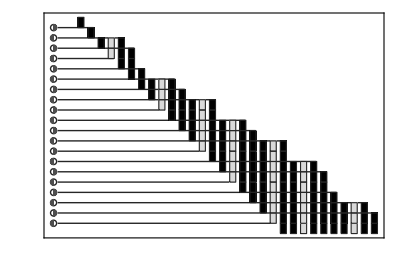

```mathematica
With[{hist=ResourceFunction["CyclicTagSystem"][{{1},{1,0,1}},{1},20],icon=Function[{pos,r,phase},{GrayLevel[.15],Circle[pos,r],GrayLevel[.3],Disk[pos,r,{Pi/2,3Pi/2}+phase π]}]},Graphics[{Table[{icon[{-1.2,-i},.3,Mod[i,2]],GrayLevel[.15],Line[{{-.8,-i},{If[hist⟦i,1⟧==0,i+.75,i+Length[hist⟦i+1⟧]+.75],-i}}]},{i,Length[hist]-1}],EdgeForm[GrayLevel[.15]],MapIndexed[{GrayLevel[.85-#1],Rectangle[{First[#2]+Last[#2]-1+.2,1-First[#2]},{First[#2]+Last[#2]-.2,-First[#2]}]}&,hist,{2}]},]]
```